Dipolar field angle: 3.4641

Abs[Ax], Abs[Ay]

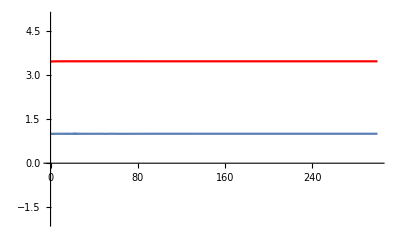

Qstokes{11.0471+0. ⅈ}

-Graphics-

Istokes{13.0606+0. ⅈ}

-Graphics-

Ustokes{6.96715+0. ⅈ}

-Graphics-

Polarization fraction{1.+0. ⅈ}

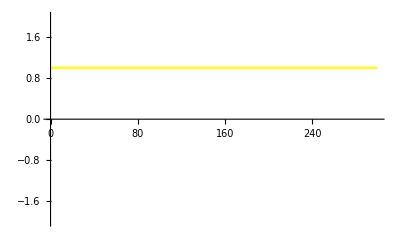

Polarization angle{0.281336+0. ⅈ}

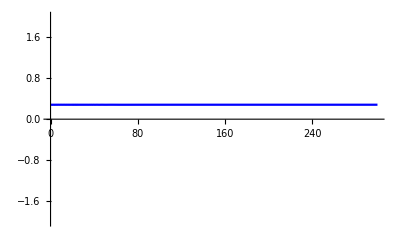

```mathematica
Clear["Global`*"]
BSurf:=1.5*10^13;
R0:=10;
angleIteration:=Pi/6;
bRep:={bRad->0,
	bTheta->0.5*BSurf*Sin[angleIteration]*(R0/(z+R0))^3,
	bPhi->BSurf*Cos[angleIteration]*(R0/(z+R0))^3};
(*0.5*BSurf*Sin[angleIteration]*(R0/(z+R0))^3*)
Bcrit:=4.4*10^13;
alpha:=1/137;

k0:=1*5.06*10^9;


mat:=ⅈ k0 delta/2 {{M,P},{P,n}};
B:={bPhi,bTheta,bRad};
Bunit:=B/Norm[B];

M:=((7 Bunit[[1]]^2 + 4 Bunit[[2]]^2)*μ[[1,1]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
n:=((4 Bunit[[1]]^2 + 7 Bunit[[2]]^2)*μ[[2,2]] - 12 delta* Bunit[[1]]^2*Bunit[[2]]^2)/(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);
P:=(3μ[[1,1]]-4 delta (4 Bunit[[1]]^2 + 7 Bunit[[2]]^2))*Bunit[[1]]*Bunit[[2]]/
(μ[[1,1]]*μ[[2,2]]-16 delta^2 *Bunit[[1]]^2*Bunit[[2]]^2);

delta:=alpha/(45 Pi)*(Norm[B]^2/Bcrit^2);

Bmatrix:=Transpose[{B}].{B}/Norm[B]^2;
beta:=Norm[B]/Bcrit;

μ:=(1+a)*IdentityMatrix[3]+m *Bmatrix;
(*a:=-2 alpha/(45 Pi)*beta^2;
m:=-4 alpha/(45 Pi)*beta^2;*)

a:=-2 alpha/(9 Pi)*Log[1+beta^2*(1+0.25487*beta^(3/4))/(5*(1+0.75*beta^(5/4)))];
m:=-alpha/(3Pi)*beta^2/(3.75+2.7*beta^(5/4)+beta^2);

Amat[z_]:={Ax[z],Ay[z]};
Amat0:={Ax[0]==3.46,Ay[0]==1};

upperLimit:=300;
eqs=NDSolve[Join[{Amat'[z]==mat.Amat[z]/.bRep},Amat0],Amat[z],{z,0,upperLimit}];


Print["Dipolar field angle: ",(B[[1]]/.bRep/.z->10)/(B[[2]]/.bRep/.z->10)];

Print["Abs[Ax], Abs[Ay]"];
p1=Plot[Abs[Evaluate[Amat[z][[1]]/.eqs]],{z,0,upperLimit},PlotRange->{{0,upperLimit},{-2,5}},PlotStyle->Red];
p2=Plot[Abs[Evaluate[Amat[z][[2]]/.eqs]],{z,0,upperLimit},PlotRange->{{0,upperLimit},{-2,5}}];
Show[p1,p2]

Istokes:=Ax[z]*Conjugate[Ax[z]]+Ay[z]*Conjugate[Ay[z]];
Qstokes:=Ax[z]*Conjugate[Ax[z]]-Ay[z]*Conjugate[Ay[z]];
Ustokes:=Ax[z]*Conjugate[Ay[z]]+Ay[z]*Conjugate[Ax[z]];

polarizationFraction:=Sqrt[Qstokes^2+Ustokes^2]/Istokes;
polarizationAngle:=1/2 ArcTan[Ustokes/Qstokes];

Print["Qstokes", Qstokes/.eqs/.z->upperLimit];
p4=Plot[Evaluate[ Qstokes/.eqs],{z,0,upperLimit},PlotRange->{{0,upperLimit},{-2,2}},PlotStyle->Yellow]

Print["Istokes", Istokes/.eqs/.z->upperLimit];
p4=Plot[Evaluate[ Istokes/.eqs],{z,0,upperLimit},PlotRange->{{0,upperLimit},{-2,2}},PlotStyle->Yellow]

Print["Ustokes", Ustokes/.eqs/.z->upperLimit];
p4=Plot[Evaluate[ Ustokes/.eqs],{z,0,upperLimit},PlotRange->{{0,upperLimit},{-2,2}},PlotStyle->Yellow]

Print["Polarization fraction", polarizationFraction/.eqs/.z->upperLimit];
p5=Plot[Evaluate[ polarizationFraction/.eqs],{z,0,upperLimit},PlotRange->{{0,upperLimit},{-2,2}},PlotStyle->Yellow]

Print["Polarization angle", polarizationAngle/.eqs/.z->upperLimit];
p6=Plot[Evaluate[ polarizationAngle/.eqs],{z,0,upperLimit},PlotRange->{{0,upperLimit},{-2,2}},PlotStyle->Blue]
```